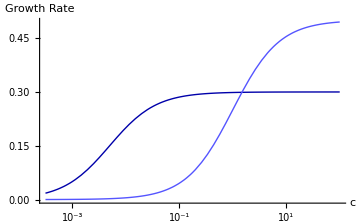

```mathematica
(*Define Monod function*)monod[c_,g_,K_]:=g*c/(K+c)

(*Parameters for the two Monod functions*)
K1=0.005;g1=0.3; (*Parameters for first function*)
K2=1.0;g2=0.5; (*Parameters for second function*)

(*Plot with a logarithmic x-axis*)
Plot[{monod[c,g1,K1],monod[c,g2,K2]},{c,10^-3.5,10^2},(*Range for substrate concentration*)PlotStyle->{{Thick,Darker[Blue]},{Thick,Lighter[Blue]}},AxesLabel->{"c","Growth Rate"},ScalingFunctions->{"Log10",None},(*Logarithmic scale for x-axis only*)LabelStyle->Directive[FontSize->12],ImageSize->Medium]
```